# True B-Spline Interpolation

## ▼ Continuous Uniform B-Spline basis function

## Spatial domain

```mathematica
𝒻CBS[n_,x_]=BSplineBasis[n-1,(x+n/2)/n];　(* 原点中心の一般的な B-Spline 基底関数 *)
```

```mathematica
Subscript[𝒻CBS, 1][x_]=Simplify[PiecewiseExpand[𝒻CBS[1,Abs[x]]]]
Subscript[𝒻CBS, 2][x_]=Simplify[PiecewiseExpand[𝒻CBS[2,Abs[x]]]]
Subscript[𝒻CBS, 3][x_]=Simplify[PiecewiseExpand[𝒻CBS[3,Abs[x]]]]
Subscript[𝒻CBS, 4][x_]=Simplify[PiecewiseExpand[𝒻CBS[4,Abs[x]]]]
Subscript[𝒻CBS, 5][x_]=Simplify[PiecewiseExpand[𝒻CBS[5,Abs[x]]]]
Subscript[𝒻CBS, 6][x_]=Simplify[PiecewiseExpand[𝒻CBS[6,Abs[x]]]]
```

Piecewise[{{1, Abs[x]≤1/2}, {0, True}}]

Piecewise[{{1-Abs[x], Abs[x]≤1}, {0, True}}]

Piecewise[{{3/4-Abs[x]^2, 2 Abs[x]<1}, {1/8 (3-2 Abs[x])^2, 1/2≤Abs[x]≤3/2}, {0, True}}]

Piecewise[{{-1/6 (-2+Abs[x])^3, 1≤Abs[x]≤2}, {1/6 (4-6 Abs[x]^2+3 Abs[x]^3), Abs[x]<1}, {0, True}}]

Piecewise[{{1/96 (55+20 Abs[x]-120 Abs[x]^2+80 Abs[x]^3-16 Abs[x]^4), 1/2≤Abs[x]<3/2}, {1/384 (5-2 Abs[x])^4, 3/2≤Abs[x]≤5/2}, {115/192-(5 Abs[x]^2)/8+Abs[x]^4/4, 2 Abs[x]<1}, {0, True}}]

Piecewise[{{1/60 (33-30 Abs[x]^2+15 Abs[x]^4-5 Abs[x]^5), Abs[x]<1}, {-1/120 (-3+Abs[x])^5, 2≤Abs[x]≤3}, {1/120 (51+75 Abs[x]-210 Abs[x]^2+150 Abs[x]^3-45 Abs[x]^4+5 Abs[x]^5), 1≤Abs[x]<2}, {0, True}}]

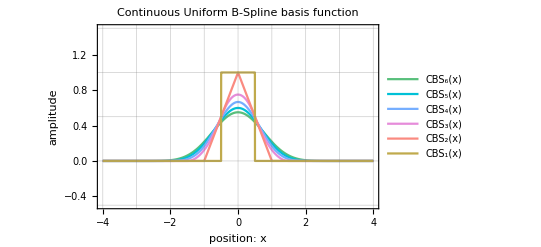

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Continuous Uniform B-Spline basis function (SD).svg

```mathematica
Subscript[gra𝒻CBS, 1]=Plot[Legended[Subscript[𝒻CBS, 1][x],"CBS_1(x)"],{x,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[192/255,170/255,076/255]}];
Subscript[gra𝒻CBS, 2]=Plot[Legended[Subscript[𝒻CBS, 2][x],"CBS_2(x)"],{x,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[250/255,138/255,128/255]}];
Subscript[gra𝒻CBS, 3]=Plot[Legended[Subscript[𝒻CBS, 3][x],"CBS_3(x)"],{x,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[230/255,140/255,218/255]}];
Subscript[gra𝒻CBS, 4]=Plot[Legended[Subscript[𝒻CBS, 4][x],"CBS_4(x)"],{x,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[117/255,174/255,255/255]}];
Subscript[gra𝒻CBS, 5]=Plot[Legended[Subscript[𝒻CBS, 5][x],"CBS_5(x)"],{x,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[000/255,193/255,215/255]}];
Subscript[gra𝒻CBS, 6]=Plot[Legended[Subscript[𝒻CBS, 6][x],"CBS_6(x)"],{x,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[088/255,191/255,123/255]}];
gra𝒻CBSs=Show[Subscript[gra𝒻CBS, 6],Subscript[gra𝒻CBS, 5],Subscript[gra𝒻CBS, 4],Subscript[gra𝒻CBS, 3],Subscript[gra𝒻CBS, 2],Subscript[gra𝒻CBS, 1],PlotLabel->"Continuous Uniform B-Spline basis function",Frame->True,FrameLabel->{"position: x","amplitude"},GridLines->{Range[-4,+4,1],Range[-0.5,+1.5,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Continuous Uniform B-Spline basis function (SD).svg"}],gra𝒻CBSs]
```

## Frequency domain

```mathematica
Subscript[ℱCBS, 1][ω_]=FullSimplify[FourierTransform[Subscript[𝒻CBS, 1][x],x,ω,FourierParameters->{1,-1}]]
Subscript[ℱCBS, 2][ω_]=FullSimplify[FourierTransform[Subscript[𝒻CBS, 2][x],x,ω,FourierParameters->{1,-1}]]
Subscript[ℱCBS, 3][ω_]=FullSimplify[FourierTransform[Subscript[𝒻CBS, 3][x],x,ω,FourierParameters->{1,-1}]]
Subscript[ℱCBS, 4][ω_]=FullSimplify[FourierTransform[Subscript[𝒻CBS, 4][x],x,ω,FourierParameters->{1,-1}]]
Subscript[ℱCBS, 5][ω_]=FullSimplify[FourierTransform[Subscript[𝒻CBS, 5][x],x,ω,FourierParameters->{1,-1}]]
Subscript[ℱCBS, 6][ω_]=FullSimplify[FourierTransform[Subscript[𝒻CBS, 6][x],x,ω,FourierParameters->{1,-1}]]
```

(2 Sin[ω/2])/ω

(2-2 Cos[ω])/ω^2

(8 Sin[ω/2]^3)/ω^3

(16 Sin[ω/2]^4)/ω^4

(32 Sin[ω/2]^5)/ω^5

(64 Sin[ω/2]^6)/ω^6

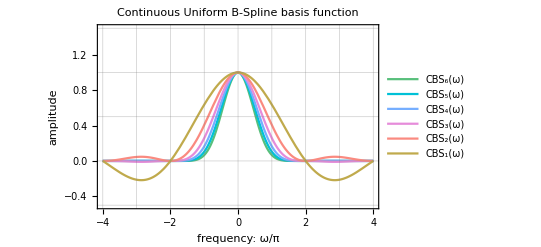

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Continuous Uniform B-Spline basis function (FD).svg

```mathematica
Subscript[graℱCBS, 1]=Plot[Legended[Subscript[ℱCBS, 1][π ω],"CBS_1(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[192/255,170/255,076/255]}];
Subscript[graℱCBS, 2]=Plot[Legended[Subscript[ℱCBS, 2][π ω],"CBS_2(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[250/255,138/255,128/255]}];
Subscript[graℱCBS, 3]=Plot[Legended[Subscript[ℱCBS, 3][π ω],"CBS_3(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[230/255,140/255,218/255]}];
Subscript[graℱCBS, 4]=Plot[Legended[Subscript[ℱCBS, 4][π ω],"CBS_4(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[117/255,174/255,255/255]}];
Subscript[graℱCBS, 5]=Plot[Legended[Subscript[ℱCBS, 5][π ω],"CBS_5(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[000/255,193/255,215/255]}];
Subscript[graℱCBS, 6]=Plot[Legended[Subscript[ℱCBS, 6][π ω],"CBS_6(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[088/255,191/255,123/255]}];
graℱCBSs=Show[Subscript[graℱCBS, 6],Subscript[graℱCBS, 5],Subscript[graℱCBS, 4],Subscript[graℱCBS, 3],Subscript[graℱCBS, 2],Subscript[graℱCBS, 1],PlotLabel->"Continuous Uniform B-Spline basis function",Frame->True,FrameLabel->{"frequency: ω/π","amplitude"},GridLines->{Range[-4,+4,1],Range[-0.5,+1.5,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Continuous Uniform B-Spline basis function (FD).svg"}],graℱCBSs]
```

Uniform B-Spline curve

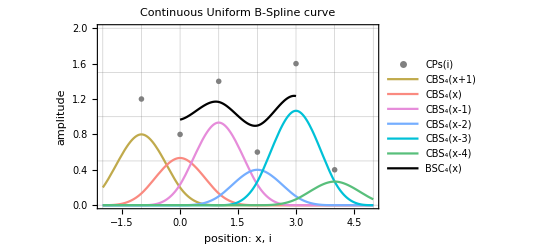

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Continuous Uniform B-Spline curve.svg

```mathematica
CPs={{-1,1.2},{0,0.8},{1,1.4},{2,0.6},{3,1.6},{4,0.4}};
𝒻BSB1[x_]:=CPs[[1,2]]*Subscript[𝒻CBS, 4][x+1];
𝒻BSB2[x_]:=CPs[[2,2]]*Subscript[𝒻CBS, 4][x];
𝒻BSB3[x_]:=CPs[[3,2]]*Subscript[𝒻CBS, 4][x-1];
𝒻BSB4[x_]:=CPs[[4,2]]*Subscript[𝒻CBS, 4][x-2];
𝒻BSB5[x_]:=CPs[[5,2]]*Subscript[𝒻CBS, 4][x-3];
𝒻BSB6[x_]:=CPs[[6,2]]*Subscript[𝒻CBS, 4][x-4];
Subscript[𝒻BSC, 4][x_]:=𝒻BSB1[x]+𝒻BSB2[x]+𝒻BSB3[x]+𝒻BSB4[x]+𝒻BSB5[x]+𝒻BSB6[x];

graCPs:=ListPlot[Legended[CPs,"CPs(i)"],PlotRange->{{-2,+5},{0,2}},PlotMarkers->"OpenMarkers",PlotStyle->{RGBColor[128/255,128/255,128/255]}]
gra𝒻BSB1=Plot[Legended[𝒻BSB1[x],"CBS_4(x+1)"],{x,-2,+5},PlotRange->{{-2,+5},{0,2}},Exclusions->None,PlotStyle->{RGBColor[192/255,170/255,076/255]}];
gra𝒻BSB2=Plot[Legended[𝒻BSB2[x],"CBS_4(x)"],{x,-2,+5},PlotRange->{{-2,+5},{0,2}},Exclusions->None,PlotStyle->{RGBColor[250/255,138/255,128/255]}];
gra𝒻BSB3=Plot[Legended[𝒻BSB3[x],"CBS_4(x-1)"],{x,-2,+5},PlotRange->{{-2,+5},{0,2}},Exclusions->None,PlotStyle->{RGBColor[230/255,140/255,218/255]}];
gra𝒻BSB4=Plot[Legended[𝒻BSB4[x],"CBS_4(x-2)"],{x,-2,+5},PlotRange->{{-2,+5},{0,2}},Exclusions->None,PlotStyle->{RGBColor[117/255,174/255,255/255]}];
gra𝒻BSB5=Plot[Legended[𝒻BSB5[x],"CBS_4(x-3)"],{x,-2,+5},PlotRange->{{-2,+5},{0,2}},Exclusions->None,PlotStyle->{RGBColor[000/255,193/255,215/255]}];
gra𝒻BSB6=Plot[Legended[𝒻BSB6[x],"CBS_4(x-4)"],{x,-2,+5},PlotRange->{{-2,+5},{0,2}},Exclusions->None,PlotStyle->{RGBColor[088/255,191/255,123/255]}];
Subscript[gra𝒻BSC, 4]=Plot[Legended[Subscript[𝒻BSC, 4][x],"BSC_4(x)"],{x,0,3},PlotRange->{{-2,+5},{0,+1.5}},Exclusions->None,PlotStyle->{RGBColor[000/255,000/255,000/255]}];
gra𝒻BSCs=Show[graCPs,gra𝒻BSB1,gra𝒻BSB2,gra𝒻BSB3,gra𝒻BSB4,gra𝒻BSB5,gra𝒻BSB6,Subscript[gra𝒻BSC, 4],PlotLabel->"Continuous Uniform B-Spline curve",Frame->True,FrameLabel->{"position: x, i","amplitude"},GridLines->{Range[-2,+6,1],Range[0,+2,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Continuous Uniform B-Spline curve.svg"}],gra𝒻BSCs]
```

## ▼ Discrete Uniform B-Spline basis function

## Spatial domain

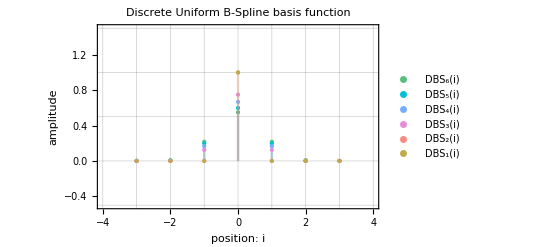

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Discrete Uniform B-Spline basis function (SD).svg

```mathematica
Subscript[gra𝒻DBS, 1]=DiscretePlot[Legended[Subscript[𝒻CBS, 1][x],"DBS_1(i)"],{x,-3,+3},PlotRange->{{-4,+4},{-0.5,+1.5}},PlotStyle->{PointSize[Medium],RGBColor[192/255,170/255,076/255]}];
Subscript[gra𝒻DBS, 2]=DiscretePlot[Legended[Subscript[𝒻CBS, 2][x],"DBS_2(i)"],{x,-3,+3},PlotRange->{{-4,+4},{-0.5,+1.5}},PlotStyle->{PointSize[Medium],RGBColor[250/255,138/255,128/255]}];
Subscript[gra𝒻DBS, 3]=DiscretePlot[Legended[Subscript[𝒻CBS, 3][x],"DBS_3(i)"],{x,-3,+3},PlotRange->{{-4,+4},{-0.5,+1.5}},PlotStyle->{PointSize[Medium],RGBColor[230/255,140/255,218/255]}];
Subscript[gra𝒻DBS, 4]=DiscretePlot[Legended[Subscript[𝒻CBS, 4][x],"DBS_4(i)"],{x,-3,+3},PlotRange->{{-4,+4},{-0.5,+1.5}},PlotStyle->{PointSize[Medium],RGBColor[117/255,174/255,255/255]}];
Subscript[gra𝒻DBS, 5]=DiscretePlot[Legended[Subscript[𝒻CBS, 5][x],"DBS_5(i)"],{x,-3,+3},PlotRange->{{-4,+4},{-0.5,+1.5}},PlotStyle->{PointSize[Medium],RGBColor[000/255,193/255,215/255]}];
Subscript[gra𝒻DBS, 6]=DiscretePlot[Legended[Subscript[𝒻CBS, 6][x],"DBS_6(i)"],{x,-3,+3},PlotRange->{{-4,+4},{-0.5,+1.5}},PlotStyle->{PointSize[Medium],RGBColor[088/255,191/255,123/255]}];
gra𝒻DBSs=Show[Subscript[gra𝒻DBS, 6],Subscript[gra𝒻DBS, 5],Subscript[gra𝒻DBS, 4],Subscript[gra𝒻DBS, 3],Subscript[gra𝒻DBS, 2],Subscript[gra𝒻DBS, 1],PlotLabel->"Discrete Uniform B-Spline basis function",Frame->True,FrameLabel->{"position: i","amplitude"},GridLines->{Range[-4,+4,1],Range[-0.5,+1.5,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Discrete Uniform B-Spline basis function (SD).svg"}],gra𝒻DBSs]
```

## Frequency domain

```mathematica
Subscript[ℱDBS, 1][ω_]=FullSimplify[FourierSequenceTransform[Subscript[𝒻CBS, 1][x],x,ω]]
Subscript[ℱDBS, 2][ω_]=FullSimplify[FourierSequenceTransform[Subscript[𝒻CBS, 2][x],x,ω]]
Subscript[ℱDBS, 3][ω_]=FullSimplify[FourierSequenceTransform[Subscript[𝒻CBS, 3][x],x,ω]]
Subscript[ℱDBS, 4][ω_]=FullSimplify[FourierSequenceTransform[Subscript[𝒻CBS, 4][x],x,ω]]
Subscript[ℱDBS, 5][ω_]=FullSimplify[FourierSequenceTransform[Subscript[𝒻CBS, 5][x],x,ω]]
Subscript[ℱDBS, 6][ω_]=FullSimplify[FourierSequenceTransform[Subscript[𝒻CBS, 6][x],x,ω]]
```

1

1

1/4 (3+Cos[ω])

1/3 (2+Cos[ω])

1/192 (115+76 Cos[ω]+Cos[2 ω])

1/60 (33+26 Cos[ω]+Cos[2 ω])

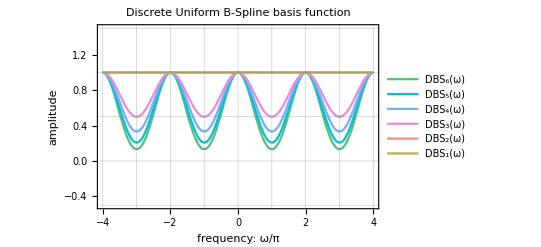

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Discrete Uniform B-Spline basis function (FD).svg

```mathematica
Subscript[graℱDBS, 1]=Plot[Legended[Subscript[ℱDBS, 1][π ω],"DBS_1(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[192/255,170/255,076/255]}];
Subscript[graℱDBS, 2]=Plot[Legended[Subscript[ℱDBS, 2][π ω],"DBS_2(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[250/255,138/255,128/255]}];
Subscript[graℱDBS, 3]=Plot[Legended[Subscript[ℱDBS, 3][π ω],"DBS_3(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[230/255,140/255,218/255]}];
Subscript[graℱDBS, 4]=Plot[Legended[Subscript[ℱDBS, 4][π ω],"DBS_4(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[117/255,174/255,255/255]}];
Subscript[graℱDBS, 5]=Plot[Legended[Subscript[ℱDBS, 5][π ω],"DBS_5(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[000/255,193/255,215/255]}];
Subscript[graℱDBS, 6]=Plot[Legended[Subscript[ℱDBS, 6][π ω],"DBS_6(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{-0.5,+1.5}},Exclusions->None,PlotStyle->{RGBColor[088/255,191/255,123/255]}];
graℱDBSs=Show[Subscript[graℱDBS, 6],Subscript[graℱDBS, 5],Subscript[graℱDBS, 4],Subscript[graℱDBS, 3],Subscript[graℱDBS, 2],Subscript[graℱDBS, 1],PlotLabel->"Discrete Uniform B-Spline basis function",Frame->True,FrameLabel->{"frequency: ω/π","amplitude"},GridLines->{Range[-4,+4,1],Range[-0.5,+1.5,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Discrete Uniform B-Spline basis function (FD).svg"}],graℱDBSs]
```

## ▼ Discrete High-Enhancement Filter function

## Frequency domain

```mathematica
Subscript[ℱDHE, 1][ω_]=1/Subscript[ℱDBS, 1][ω]
Subscript[ℱDHE, 2][ω_]=1/Subscript[ℱDBS, 2][ω]
Subscript[ℱDHE, 3][ω_]=1/Subscript[ℱDBS, 3][ω]
Subscript[ℱDHE, 4][ω_]=1/Subscript[ℱDBS, 4][ω]
Subscript[ℱDHE, 5][ω_]=1/Subscript[ℱDBS, 5][ω]
Subscript[ℱDHE, 6][ω_]=1/Subscript[ℱDBS, 6][ω]
```

1

1

4/(3+Cos[ω])

3/(2+Cos[ω])

192/(115+76 Cos[ω]+Cos[2 ω])

60/(33+26 Cos[ω]+Cos[2 ω])

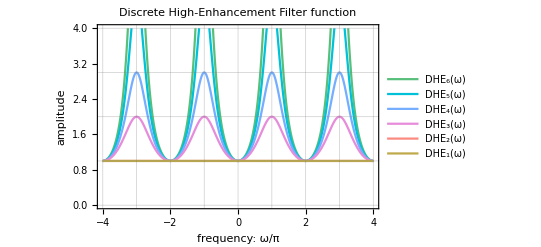

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Discrete High-Enhancement Filter function (FD).svg

```mathematica
Subscript[graℱDHE, 1]= Plot[Legended[Subscript[ℱDHE, 1][π ω],"DHE_1(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[192/255,170/255,076/255]}];
Subscript[graℱDHE, 2]= Plot[Legended[Subscript[ℱDHE, 2][π ω],"DHE_2(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[250/255,138/255,128/255]}];
Subscript[graℱDHE, 3]= Plot[Legended[Subscript[ℱDHE, 3][π ω],"DHE_3(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[230/255,140/255,218/255]}];
Subscript[graℱDHE, 4]= Plot[Legended[Subscript[ℱDHE, 4][π ω],"DHE_4(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[117/255,174/255,255/255]}];
Subscript[graℱDHE, 5]= Plot[Legended[Subscript[ℱDHE, 5][π ω],"DHE_5(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[000/255,193/255,215/255]}];
Subscript[graℱDHE, 6]= Plot[Legended[Subscript[ℱDHE, 6][π ω],"DHE_6(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[088/255,191/255,123/255]}];
graℱDHEs=Show[Subscript[graℱDHE, 6],Subscript[graℱDHE, 5],Subscript[graℱDHE, 4],Subscript[graℱDHE, 3],Subscript[graℱDHE, 2],Subscript[graℱDHE, 1],PlotLabel->"Discrete High-Enhancement Filter function", Frame->True, FrameLabel->{"frequency: ω/π","amplitude"},GridLines->{Range[-4,+4,1],Range[0,4,1]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Discrete High-Enhancement Filter function (FD).svg"}],graℱDHEs]
```

## Spatial domain

```mathematica
Subscript[𝒻DHE, 1][i_]=FourierCosCoefficient[Subscript[ℱDHE, 1][ω],ω,i]/2
Subscript[𝒻DHE, 2][i_]=FourierCosCoefficient[Subscript[ℱDHE, 2][ω],ω,i]/2
Subscript[𝒻DHE, 3][i_]=FourierCosCoefficient[Subscript[ℱDHE, 3][ω],ω,i]/2
Subscript[𝒻DHE, 4][i_]=FourierCosCoefficient[Subscript[ℱDHE, 4][ω],ω,i]/2
```

DiscreteDelta[i]

DiscreteDelta[i]

2 HypergeometricPFQRegularized[{1/2,1,1},{1-i,1+i},-1]

3 HypergeometricPFQRegularized[{1/2,1,1},{1-i,1+i},-2]

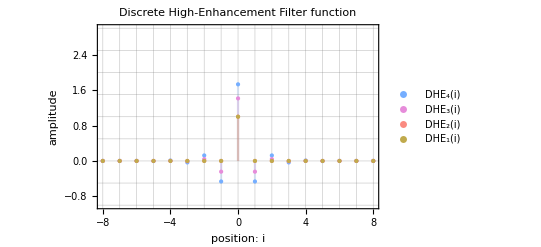

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Discrete High-Enhancement Filter function (SD).svg

```mathematica
Subscript[gra𝒻DHE, 1]=DiscretePlot[Legended[Subscript[𝒻DHE, 1][i],"DHE_1(i)"],{i,-8,+8},PlotRange->{{-8,+8},{-1,+3}},PlotStyle->{PointSize[Medium],RGBColor[192/255,170/255,076/255]}];
Subscript[gra𝒻DHE, 2]=DiscretePlot[Legended[Subscript[𝒻DHE, 2][i],"DHE_2(i)"],{i,-8,+8},PlotRange->{{-8,+8},{-1,+3}},PlotStyle->{PointSize[Medium],RGBColor[250/255,138/255,128/255]}];
Subscript[gra𝒻DHE, 3]=DiscretePlot[Legended[Subscript[𝒻DHE, 3][i],"DHE_3(i)"],{i,-8,+8},PlotRange->{{-8,+8},{-1,+3}},PlotStyle->{PointSize[Medium],RGBColor[230/255,140/255,218/255]}];
Subscript[gra𝒻DHE, 4]=DiscretePlot[Legended[Subscript[𝒻DHE, 4][i],"DHE_4(i)"],{i,-8,+8},PlotRange->{{-8,+8},{-1,+3}},PlotStyle->{PointSize[Medium],RGBColor[117/255,174/255,255/255]}];
gra𝒻DHEs=Show[Subscript[gra𝒻DHE, 4],Subscript[gra𝒻DHE, 3],Subscript[gra𝒻DHE, 2],Subscript[gra𝒻DHE, 1],PlotLabel->"Discrete High-Enhancement Filter function",Frame->True,FrameLabel->{"position: i","amplitude"},GridLines->{Range[-8,+8,1],Range[-1,+3,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Discrete High-Enhancement Filter function (SD).svg"}],gra𝒻DHEs]
```

## ▼ Continuous High-Enhancement Filter function

```mathematica
Subscript[abs𝒻CHE, 3][x_]=Subscript[𝒻DHE, 3][0]Exp[Log[-Subscript[𝒻DHE, 3][1]/Subscript[𝒻DHE, 3][0]]Abs[x]]
Subscript[abs𝒻CHE, 4][x_]=Subscript[𝒻DHE, 4][0]Exp[Log[-Subscript[𝒻DHE, 4][1]/Subscript[𝒻DHE, 4][0]]Abs[x]]
```

2^(1/2-Abs[x]/2) (-4+3 √2)^Abs[x]

3^(1/2-Abs[x]/2) (-3+2 √3)^Abs[x]

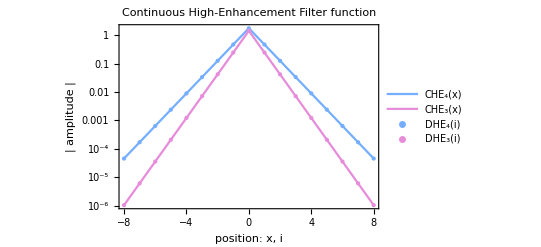

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Continuous High-Enhancement Filter function (AbsSD).svg

```mathematica
rangeN :=8;
Subscript[graAbs𝒻CHE, 3]=LogPlot[Legended[Subscript[abs𝒻CHE, 3][i],"CHE_3(x)"],{i,-rangeN,+rangeN},PlotRange->{{-rangeN,+rangeN},{10^+1,10^-rangeN}},GridLines->{Range[-rangeN,+rangeN],Table[10^n,{n,-rangeN,+1}]},PlotStyle->{RGBColor[230/255,140/255,218/255]}];
Subscript[graAbs𝒻CHE, 4]=LogPlot[Legended[Subscript[abs𝒻CHE, 4][i],"CHE_4(x)"],{i,-rangeN,+rangeN},PlotRange->{{-rangeN,+rangeN},{10^+1,10^-rangeN}},GridLines->{Range[-rangeN,+rangeN],Table[10^n,{n,-rangeN,+1}]},PlotStyle->{RGBColor[117/255,174/255,255/255]}];
Subscript[graAbs𝒻DHE, 3]=ListLogPlot[Legended[Table[{i,Abs[Subscript[𝒻DHE, 3][i]]},{i,-rangeN,+rangeN}],"DHE_3(i)"],PlotRange->{{-rangeN,+rangeN},{10^+1,10^-rangeN}},GridLines->{Range[-rangeN,+rangeN],Table[10^n,{n,-rangeN,+1}]},PlotStyle->{PointSize[Medium],RGBColor[230/255,140/255,218/255]}];
Subscript[graAbs𝒻DHE, 4]=ListLogPlot[Legended[Table[{i,Abs[Subscript[𝒻DHE, 4][i]]},{i,-rangeN,+rangeN}],"DHE_4(i)"],PlotRange->{{-rangeN,+rangeN},{10^+1,10^-rangeN}},GridLines->{Range[-rangeN,+rangeN],Table[10^n,{n,-rangeN,+1}]},PlotStyle->{PointSize[Medium],RGBColor[117/255,174/255,255/255]}];
graAbs𝒻DHEs=Show[Subscript[graAbs𝒻CHE, 4],Subscript[graAbs𝒻CHE, 3],Subscript[graAbs𝒻DHE, 4],Subscript[graAbs𝒻DHE, 3],PlotLabel->"Continuous High-Enhancement Filter function", Frame->True, FrameLabel->{"position: x, i","| amplitude |"}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Continuous High-Enhancement Filter function (AbsSD).svg"}],graAbs𝒻DHEs]
```

```mathematica
Subscript[𝒻CHE, 3][x_]=(-1)^Abs[x] Subscript[abs𝒻CHE, 3][x]
Subscript[𝒻CHE, 4][x_]=(-1)^Abs[x] Subscript[abs𝒻CHE, 4][x]
```

2^(1/2-Abs[x]/2) (4-3 √2)^Abs[x]

3^(1/2-Abs[x]/2) (3-2 √3)^Abs[x]

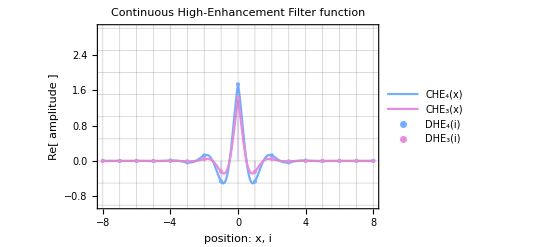

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Continuous High-Enhancement Filter function (SD).svg

```mathematica
Subscript[gra𝒻CHE, 3]=Plot[Legended[Re[Subscript[𝒻CHE, 3][x]],"CHE_3(x)"],{x,-rangeN,+rangeN},PlotRange->{{-rangeN,+rangeN},{-1,+3}},PlotStyle->{RGBColor[230/255,140/255,218/255]}];
Subscript[gra𝒻CHE, 4]=Plot[Legended[Re[Subscript[𝒻CHE, 4][x]],"CHE_4(x)"],{x,-rangeN,+rangeN},PlotRange->{{-rangeN,+rangeN},{-1,+3}},PlotStyle->{RGBColor[117/255,174/255,255/255]}];
gra𝒻CHEs=Show[Subscript[gra𝒻CHE, 4],Subscript[gra𝒻CHE, 3],Subscript[gra𝒻DHE, 4],Subscript[gra𝒻DHE, 3],PlotLabel->"Continuous High-Enhancement Filter function", Frame->True, FrameLabel->{"position: x, i","Re[ amplitude ]"},GridLines->{Range[-8,+8,1],Range[-1,+3,0.5]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Continuous High-Enhancement Filter function (SD).svg"}],gra𝒻CHEs]
```

## ▼ Approximate Discrete High-Enhancement Filter

## Spatial domain

```mathematica
tapN :=8;
```

```mathematica
Subscript[tapAHE, 1]=Table[Subscript[𝒻DHE, 1][i],{i,0,tapN}]
Subscript[tapAHE, 2]=Table[Subscript[𝒻DHE, 2][i],{i,0,tapN}]
Subscript[tapAHE, 3]=Table[Subscript[𝒻DHE, 3][i],{i,0,tapN}]
Subscript[tapAHE, 4]=Table[Subscript[𝒻DHE, 4][i],{i,0,tapN}]
```

{1,0,0,0,0,0,0,0,0}

{1,0,0,0,0,0,0,0,0}

{√2,4-3 √2,-24+17 √2,140-99 √2,-816+577 √2,4756-3363 √2,-27720+19601 √2,161564-114243 √2,-941664+665857 √2}

{√3,3-2 √3,-12+7 √3,45-26 √3,-168+97 √3,627-362 √3,-2340+1351 √3,8733-5042 √3,-32592+18817 √3}

```mathematica
Subscript[𝒻AHE, 1][i_]=If[-tapN≤i≤+tapN,Subscript[tapAHE, 1][[1+Abs[i]]],0];
Subscript[𝒻AHE, 2][i_]=If[-tapN≤i≤+tapN,Subscript[tapAHE, 2][[1+Abs[i]]],0];
Subscript[𝒻AHE, 3][i_]=If[-tapN≤i≤+tapN,Subscript[tapAHE, 3][[1+Abs[i]]],0];
Subscript[𝒻AHE, 4][i_]=If[-tapN≤i≤+tapN,Subscript[tapAHE, 4][[1+Abs[i]]],0];
```

## Frequency domain

```mathematica
Subscript[ℱAHE, 1][ω_]=FullSimplify[FourierSequenceTransform[Subscript[𝒻AHE, 1][i],i,ω]]
Subscript[ℱAHE, 2][ω_]=FullSimplify[FourierSequenceTransform[Subscript[𝒻AHE, 2][i],i,ω]]
Subscript[ℱAHE, 3][ω_]=FullSimplify[FourierSequenceTransform[Subscript[𝒻AHE, 3][i],i,ω]]
Subscript[ℱAHE, 4][ω_]=FullSimplify[FourierSequenceTransform[Subscript[𝒻AHE, 4][i],i,ω]]
```

1

1

√2+(8-6 √2) Cos[ω]+(-48+34 √2) Cos[2 ω]+2 (140-99 √2) Cos[3 ω]+2 (-816+577 √2) Cos[4 ω]+(9512-6726 √2) Cos[5 ω]+2 (-27720+19601 √2) Cos[6 ω]+2 (161564-114243 √2) Cos[7 ω]+2 (-941664+665857 √2) Cos[8 ω]

√3+(6-4 √3) Cos[ω]+2 (-12+7 √3) Cos[2 ω]+(90-52 √3) Cos[3 ω]+2 (-168+97 √3) Cos[4 ω]+2 (627-362 √3) Cos[5 ω]+(-4680+2702 √3) Cos[6 ω]+2 (8733-5042 √3) Cos[7 ω]+2 (-32592+18817 √3) Cos[8 ω]

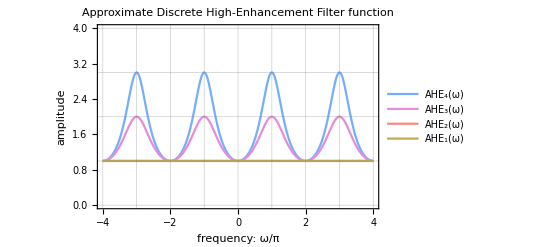

P:\» LUXOPHIA\» DEMO\・BSplineInterpolation\--------\_README\Approximate Discrete High-Enhancement Filter function (FD).svg

```mathematica
Subscript[graℱAHE, 1]= Plot[Legended[Subscript[ℱAHE, 1][π ω],"AHE_1(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[192/255,170/255,076/255]}];
Subscript[graℱAHE, 2]= Plot[Legended[Subscript[ℱAHE, 2][π ω],"AHE_2(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[250/255,138/255,128/255]}];
Subscript[graℱAHE, 3]= Plot[Legended[Subscript[ℱAHE, 3][π ω],"AHE_3(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[230/255,140/255,218/255]}];
Subscript[graℱAHE, 4]= Plot[Legended[Subscript[ℱAHE, 4][π ω],"AHE_4(ω)"],{ω,-4,+4},PlotRange->{{-4,+4},{0,+4}},Exclusions ->None,PlotStyle->{RGBColor[117/255,174/255,255/255]}];
graℱAHEs=Show[Subscript[graℱAHE, 4],Subscript[graℱAHE, 3],Subscript[graℱAHE, 2],Subscript[graℱAHE, 1],PlotLabel->"Approximate Discrete High-Enhancement Filter function", Frame->True, FrameLabel->{"frequency: ω/π","amplitude"},GridLines->{Range[-4,+4,1],Range[0,4,1]}]
Export[FileNameJoin[{NotebookDirectory[],"_README/Approximate Discrete High-Enhancement Filter function (FD).svg"}],graℱAHEs]
```